```mathematica
ExpPrint[exp_]:=Block[
{t=Table[exp[[k]],{k,1,Length[exp]}], cellformat},
cellformat=Framed[TextCell[#,CellSize->{550,Automatic}, TextAlignment->Left,FontSize->12]]&;
t=Map[cellformat,Sort[t,ExpComp]];
TableForm[t]
]
```

```mathematica
SameEdges[g_,h_]:=Block[{result=True},
If[EdgeCount[g]!=EdgeCount[h],Return[False]];
Table[If[!EdgeQ[g,e],result=False],{e,EdgeList[h]}];
result
]
```

```mathematica
SameVertices[g_,h_]:=Block[{result=True},
If[VertexCount[g]!=VertexCount[h],Return[False]];
Table[If[!VertexQ[g,v],result=False],{v,VertexList[h]}];
result
]
```

```mathematica
FindGraph[g_]:=Block[{isomorph},
isomorph=Select[Keys[stubbornForm4],
With[{h=stubbornForm4[#,"graph"]},
IsomorphicGraphQ[g,h]&&
SameEdges[g,h]&&
SameVertices[g,h]
]&];
First[isomorph]
]
```

```mathematica
FindGraph[CycleGraph[4]]
```

120

```mathematica
AddEdge[g_,code_,vertices_]:=Block[{h=g,decoded=PadLeft[IntegerDigits[code,2],3,0],i},
If[decoded[[1]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[2]]]];
If[decoded[[2]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[3]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[2]]<->vertices[[3]]]];
h
]
```

```mathematica
FindRelations[g_,verticesg_,h_,verticesh_]:=Block[{g2,h2,keyg,keyh},
Table[
g2=AddEdge[g,code,verticesg];
h2=AddEdge[h,code,verticesh];
keyg=FindGraph[g2];
keyh=FindGraph[h2];
(*Print[Graph[g2,VertexLabels->"Name"],keyg,Graph[h2,VertexLabels->"Name"],keyh];*)
{keyg,keyh}
,{code,0,7}
]
]
```

```mathematica
FindRelations[Graph[{1,2,3,4},{1<->2,1<->4}],{2,3,4},Graph[{1,2,3,4},{1<->2,1<->4}],{2,3,4}]
```

{{270,270},{271,271},{273,273},{274,274},{279,279},{280,280},{282,282},{283,283}}

```mathematica
Clear[Compare4]
```

```mathematica
Compare4[270,270]
```

{-β+λ==-bb+ll,1/2 (v01+v04-v06+v10+2 β-2 λ)==1/2 (2 bb-2 ll+y01+y04-y06+y10),1/2 (v01+v02+2 v04-v05-2 v06-v07+2 v11+2 α+2 β-6 λ)==1/2 (2 aa+2 bb-6 ll+y01+y02+2 y04-y05-2 y06-y07+2 y11),1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)==1/2 (-2 aa-2 bb+6 ll-y02-y04+y05+y06+y07+y10-2 y11),1/2 (v01-v02+v05+v07-2 v11-2 β+2 λ)==1/2 (-2 bb+2 ll+y01-y02+y05+y07-2 y11),1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)==1/2 (2 bb-2 ll+y02+y04-y05-y06-y07+y10+2 y11)}

```mathematica
ColorTablePrint[282,stubbornForm4,"colofour3","colortable3"]
```

-Graphics-2821/2 (4 s01+4 s02+2 s03+2 s04-v02-v04+v05+v06+v07+v10-2 v11)Greater
( | = | ≠
1<->2 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
1<->3 | α-ζ | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+2 ζ+4 λ)
1<->4 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
2<->3 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
2<->4 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
3<->4 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ) | α)

```mathematica
stubbornForm4[4]["graph"]//EdgeList
```

{2<->4,3<->4}

```mathematica
Clear[Compare4]
```

```mathematica
repfours={z->Z,s01->x01,s02->x02,s03->x03,s04->x04,v01->y01,v02->y02,v03->y03,v04->y04,v05->y05,v06->y06,v07->y07,v10->y10,v11->y11,v12->y12,α->aa,β->bb,λ->ll,α1->aa1,ζ->zz}
```

{z→Z,s01→x01,s02→x02,s03→x03,s04→x04,v01→y01,v02→y02,v03→y03,v04→y04,v05→y05,v06→y06,v07→y07,v10→y10,v11→y11,v12→y12,α→aa,β→bb,λ→ll,α1→aa1,ζ→zz}

```mathematica
Compare4[number4_,yyy_,colofour_:"colofour3",colortable_:"colortable4"]:=Block[
{current4=stubbornForm4[number4],current5=stubbornForm4[yyy], result={}, table4,table5, title, title2,cellformat},
table4=current4[colortable];
table5=current5[colortable];
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{280,Automatic}, TextAlignment->Center,FontSize->11]&;
title=cellformat[With[{t=ToString[stubbornForm4[number4]["comp"]]},Style[stubbornForm4[number4][colofour],If[t=="Greater",Darker[Darker[Green]],Red]]]];
title2=cellformat[With[{t=ToString[stubbornForm4[yyy]["comp"]]},Style[stubbornForm4[yyy][colofour],If[t=="Greater",Darker[Darker[Green]],Red]]]];
Print[Labeled[
Graph[current4["graph"]
 ,ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title,Style[number4,Bold,Underlined]},{Bottom,Top}]
->Labeled[
Graph[current5["graph"],ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title2,Style[yyy,Bold,Underlined]},{Bottom,Top}]];
Print[ColorTablePrint[number4,stubbornForm4,colofour,colortable]
];
Table[
AppendTo[result,(table4[[ind,1]])==(table5[[ind,1]]/.repfours)];
AppendTo[result,(table4[[ind,2]])==(table5[[ind,2]]/.repfours)];,
{ind,{4,5,6}}
];
Print[ExpPrint[Fold[And,DeleteDuplicates[result]]]];
result
]
```

```mathematica
FindRelations[Graph[{1,2,3,4},{1<->2,1<->4}],{2,3,4},Graph[{1,2,3,4},{1<->2,1<->3,1<->4}],{2,3,4}]
```

{{270,351},{271,352},{273,354},{274,355},{279,360},{280,361},{282,363},{283,364}}

```mathematica
{1,1},{3,2}
```

```mathematica
TableForm[stubbornForm4[30]["colortable3"]]
```

1/2 (-v01+v04+v06-v10) | v10
1/2 (-v01-v02+v05+2 v06+v07-2 v11-2 v12-2 β-2 ζ+6 λ) | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 v12+2 β+2 ζ-6 λ)
0 | 1/2 (-v01+v04+v06+v10)
1/2 (-v01+v04+v06+v10-2 v12-2 α+2 λ) | v12+α-λ
0 | 1/2 (-v01+v04+v06+v10)
1/2 (-2 v01-v02-2 v03-v04+3 v05+3 v06+v07+v10-2 v11-2 v12-4 α-4 β+10 λ) | v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12+2 α+2 β-5 λ

```mathematica
TableForm[stubbornForm4[28]["colortable4"]]
```

1/2 (-6 s01-4 s02-4 s03-2 s04+v01+2 v03+v04-2 v05-v06-v10+2 v12) | 1/2 (-2 s01-2 s02+v02+v04-v05-v06-v07+v10+2 v11)
1/2 (8 s01+6 s02+4 s03+2 s04-v01-v02+v05+2 v06+v07-2 v11-2 v12) | -8 s01-6 s02-4 s03-2 s04+v01+v02+v03+v04-2 v05-2 v06-v07+2 v11+2 v12
0 | s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12
1/2 (2 s01+2 s03-v01+v04+v06+v10-2 v12) | 1/2 (-10 s01-6 s02-6 s03-2 s04+2 v01+v02+2 v03+v04-3 v05-3 v06-v07-v10+2 v11+4 v12)
s01+s03 | -5 s01-3 s02-3 s03-s04+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12
0 | s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12

```mathematica
eqs=Flatten[Map[Compare4[#[[1]],#[[2]]]&,FindRelations[Graph[{1,2,3,4},{1<->2,1<->4}],{2,3,4},Graph[{1,2,3,4},{1<->2,1<->4}],{2,3,4}]]];
```

-Graphics-1/2 (v01+v04-v06+v10)270→-Graphics-1/2 (v01+v04-v06+v10)270

-Graphics-2701/2 (v01+v04-v06+v10)Greater
( | = | ≠
1<->2 | 0 | 1/2 (v01+v04-v06+v10)
1<->3 | -β+λ | 1/2 (v01+v04-v06+v10+2 β-2 λ)
1<->4 | 0 | 1/2 (v01+v04-v06+v10)
2<->3 | 1/2 (v01+v02+2 v04-v05-2 v06-v07+2 v11+2 α+2 β-6 λ) | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)
2<->4 | 1/2 (v01+v04-v06-v10) | v10
3<->4 | 1/2 (v01-v02+v05+v07-2 v11-2 β+2 λ) | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ))

v10==y10
1/2 (v01+v04-v06-v10)==1/2 (y01+y04-y06-y10)
1/2 (v01-v02+v05+v07-2 v11-2 β+2 λ)==1/2 (-2 bb+2 ll+y01-y02+y05+y07-2 y11)
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)==1/2 (2 bb-2 ll+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (v01+v02+2 v04-v05-2 v06-v07+2 v11+2 α+2 β-6 λ)==1/2 (2 aa+2 bb-6 ll+y01+y02+2 y04-y05-2 y06-y07+2 y11)
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)==1/2 (-2 aa-2 bb+6 ll-y02-y04+y05+y06+y07+y10-2 y11)

-Graphics-1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)271→-Graphics-1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)271

-Graphics-2711/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)
1<->3 | -β+λ | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+4 β-4 λ)
1<->4 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)
2<->3 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-4 λ) | λ
2<->4 | -α+λ | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)
3<->4 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ))

λ==ll
-α+λ==-aa+ll
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-2 λ)==1/2 (2 bb-2 ll+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-4 λ)==1/2 (2 bb-4 ll+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)==1/2 (2 aa+2 bb-4 ll+y02+y04-y05-y06-y07+y10+2 y11)

-Graphics-v10273→-Graphics-v10273

-Graphics-273v10Greater
( | = | ≠
1<->2 | 0 | v10
1<->3 | α-ζ | v10-α+ζ
1<->4 | 0 | v10
2<->3 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-4 λ) | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
2<->4 | 0 | v10
3<->4 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ) | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ))

v10==y10
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-4 λ)==1/2 (2 bb-4 ll+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)==1/2 (-2 bb+4 ll-y02-y04+y05+y06+y07+y10-2 y11)
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)==1/2 (2 aa+2 bb-4 ll+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ)==1/2 (-2 aa-2 bb+4 ll-y02-y04+y05+y06+y07+y10-2 y11)

-Graphics-1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)274→-Graphics-1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)274

-Graphics-2741/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)
1<->3 | α-ζ | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β+2 ζ-4 λ)
1<->4 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)
2<->3 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-4 λ) | α
2<->4 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)
3<->4 | 0 | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ))

α==aa
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 β-4 λ)==1/2 (2 bb-4 ll+y02+y04-y05-y06-y07+y10+2 y11)
1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 α+2 β-4 λ)==1/2 (2 aa+2 bb-4 ll+y02+y04-y05-y06-y07+y10+2 y11)

-Graphics-1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)279→-Graphics-1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)279

-Graphics-2791/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)
1<->3 | -β+λ | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α+4 λ)
1<->4 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)
2<->3 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)
2<->4 | -α+λ | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
3<->4 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ) | λ)

λ==ll
-α+λ==-aa+ll
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)==1/2 (-2 bb+4 ll-y02-y04+y05+y06+y07+y10-2 y11)
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ)==1/2 (-2 aa-2 bb+4 ll-y02-y04+y05+y06+y07+y10-2 y11)
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+6 λ)==1/2 (-2 aa-2 bb+6 ll-y02-y04+y05+y06+y07+y10-2 y11)

-Graphics-λ280→-Graphics-λ280

-Graphics-280λGreater
( | = | ≠
1<->2 | 0 | λ
1<->3 | -β+λ | β
1<->4 | 0 | λ
2<->3 | 0 | λ
2<->4 | -α+λ | α
3<->4 | 0 | λ)

α==aa
λ==ll
-α+λ==-aa+ll

-Graphics-1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)282→-Graphics-1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)282

-Graphics-2821/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
1<->3 | α-ζ | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+2 ζ+4 λ)
1<->4 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
2<->3 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
2<->4 | 0 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)
3<->4 | 1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ) | α)

α==aa
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 β+4 λ)==1/2 (-2 bb+4 ll-y02-y04+y05+y06+y07+y10-2 y11)
1/2 (-v02-v04+v05+v06+v07+v10-2 v11-2 α-2 β+4 λ)==1/2 (-2 aa-2 bb+4 ll-y02-y04+y05+y06+y07+y10-2 y11)

-Graphics-α283→-Graphics-α283

-Graphics-283αGreater
( | = | ≠
1<->2 | 0 | α
1<->3 | α-ζ | ζ
1<->4 | 0 | α
2<->3 | 0 | α
2<->4 | 0 | α
3<->4 | 0 | α)

Sort::normal: Nonatomic expression expected at position 1 in Sort[α, SymbolComp].

Sort::normal: Nonatomic expression expected at position 1 in Sort[aa, SymbolComp].

Sort::normal: Nonatomic expression expected at position 1 in Sort["\[Alpha]000", "Somp"].

General::stop: Further output of Sort :: normal will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[Sort["\[Alpha]000", "Somp"]].

StringJoin::string: String expected at position 1 in StringJoin[Sort["a00a", "Somp"]].

aa
α

```mathematica
ExpressionToTableLoc[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]],{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
ExpPrint[Simplify[Fold[And,eqs]]]
```

aa==α
ll==λ
v10==y10
aa+λ==ll+α
v01+v04+y06+y10==v06+v10+y01+y04
2 bb+v01+v05+v07+y02+2 y11+2 λ==2 ll+v02+2 v11+y01+y05+y07+2 β
2 bb+v05+v06+v07+y02+y04+y10+2 y11+4 λ==4 ll+v02+v04+v10+2 v11+y05+y06+y07+2 β
2 bb+v05+v06+v07+y02+y04+y10+2 y11+2 λ==2 ll+v02+v04+v10+2 v11+y05+y06+y07+2 β
2 bb+v05+v06+v07+v10+y02+y04+2 y11+4 λ==4 ll+v02+v04+2 v11+y05+y06+y07+y10+2 β
2 aa+2 bb+v05+2 v06+v07+y01+y02+2 y04+2 y11+6 λ==6 ll+v01+v02+2 v04+2 v11+y05+2 y06+y07+2 α+2 β
2 aa+2 bb+v05+v06+v07+y02+y04+y10+2 y11+4 λ==4 ll+v02+v04+v10+2 v11+y05+y06+y07+2 α+2 β
2 aa+2 bb+v05+v06+v07+v10+y02+y04+2 y11+4 λ==4 ll+v02+v04+2 v11+y05+y06+y07+y10+2 α+2 β
2 aa+2 bb+v05+v06+v07+v10+y02+y04+2 y11+6 λ==6 ll+v02+v04+2 v11+y05+y06+y07+y10+2 α+2 β

```mathematica
Reduce[Fold[And,eqs],{α,β,λ}]//ExpressionToTableLoc
```

α==aa
λ==ll
v10==y10
v01==-v04+v06+y01+y04-y06
β==bb-v02/2-v04/2+v05/2+v06/2+v07/2-v11+y02/2+y04/2-y05/2-y06/2-y07/2+y11

```mathematica
Simplify[-s04+v02/2+v04/2-v05/2-v06/2-v07/2+v11-v12-(11 x01)/2-(7 x02)/2-2 x03+y01+y02/4+y03+y04/4-(5 y05)/4-(5 y06)/4-y07/4-(3 y10)/4+y11/2+2 y12==0]
```

4 s04+2 v05+2 v06+2 v07+4 v12+22 x01+14 x02+8 x03+5 y05+5 y06+y07+3 y10==2 v02+2 v04+4 v11+4 y01+y02+4 y03+y04+2 y11+8 y12

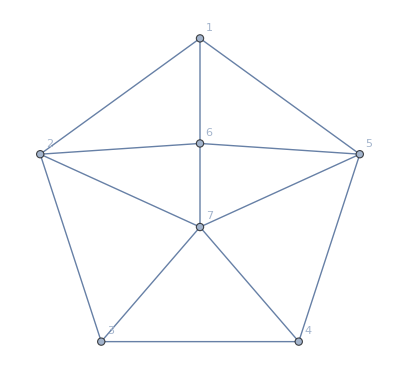

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,5<->6,6<->7,7<->3,7<->4,2<->7,5<->7},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,5<->6,6<->7,7<->3,7<->4,2<->7,5<->7},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]//GraphEmbedding
```

```mathematica
{{5.551115123125783*^-18,-0.1253658486296072},{-8.326672684688674*^-17,0.37317075685196444},{0.9510565162951535,0.3090169943749475},{0.5877852522924731,-0.8090169943749473}}
```

```mathematica
{{-8.326672684688674*^-17,0.37317075685196444},{5.551115123125783*^-18,-0.1253658486296072},{0.9510565162951535,0.3090169943749475},{-1.8369701987210297*^-16,1.}}
```

{{-1.83697×10^-16,1.},{-0.951057,0.309017},{-0.587785,-0.809017},{0.587785,-0.809017},{0.951057,0.309017},{-8.32667×10^-17,0.373171},{5.55112×10^-18,-0.125366}}